```mathematica
Vinf={1,0};
```

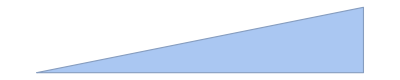

```mathematica
Rdots={{-1,0.1},{1,1/2},{1,0.1}};
Rarea=ConvexHullMesh[Rdots]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
curlDeploy=1.01Rdots;
```

```mathematica
(({{0, -1}, {1, 0}}).(Rmids[[1]]-curlDeploy[[1]]))/(2π(Rmids[[1]]-curlDeploy[[1]]).(Rmids[[1]]-curlDeploy[[1]]))
```

{-0.0298875,0.15169}

```mathematica
L1=Table[((({{0, -1}, {1, 0}}).(Rmids[[i]]-curlDeploy[[j]]))/(2π(Rmids[[i]]-curlDeploy[[j]]).(Rmids[[i]]-curlDeploy[[j]]))).Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
```

```mathematica
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
```

```mathematica
f0=Rnormals.Vinf;
```

```mathematica
L1.newGamma+r
```

{{r+0.315336 G[1]-0.314976 G[2]-0.291426 G[3]},{r-0.00310531 G[1]+0.309809 G[2]-0.319104 G[3]},{r-0.315158 G[1]+0.271503 G[2]+0.315158 G[3]}}

```mathematica
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]]
```

{{G[1]→0.340802,G[2]→-1.07425,G[3]→0.733447,r→0.167916}}

```mathematica
curlDeploy
```

{{-1.01,0.101},{1.01,0.505},{1.01,0.101}}

```mathematica
(*по-хорошему на данном этапе нужно перекидывать новые вихри в единую пачку с остальными, но пока что мы этого делать не будем, потому что такой пачки у нас нет)) *)
```

```mathematica
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution
```

{0.340802,-1.07425,0.733447,0.167916}

```mathematica
Vinf+Sum[nGammaR[[i]](({{0, -1}, {1, 0}}).({x,y}-curlDeploy[[i]]))/(2π({x,y}-curlDeploy[[i]]).({x,y}-curlDeploy[[i]])),{i,Length@nGammaR-1}]
```

{1+(0.116732 (0.101-y))/((-1.01+x)^2+(-0.101+y)^2)+(0.0542403 (0.101-y))/((1.01+x)^2+(-0.101+y)^2)-(0.170972 (0.505-y))/((-1.01+x)^2+(-0.505+y)^2),-(0.170972 (-1.01+x))/((-1.01+x)^2+(-0.505+y)^2)+(0.116732 (-1.01+x))/((-1.01+x)^2+(-0.101+y)^2)+(0.0542403 (1.01+x))/((1.01+x)^2+(-0.101+y)^2)}

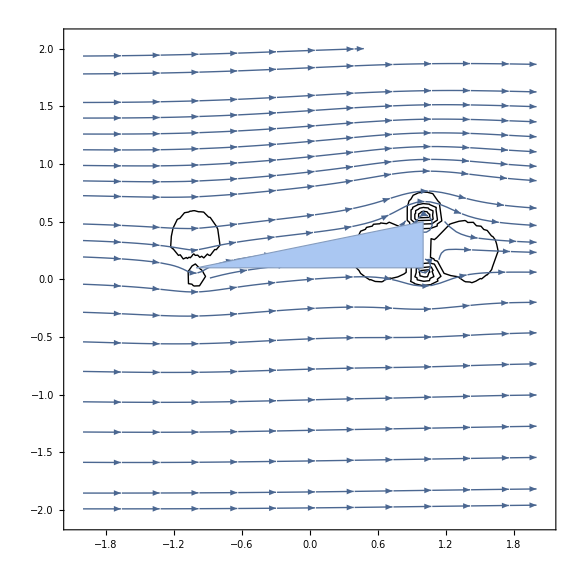

```mathematica
Show[StreamPlot[%66,{x,-2,2},{y,-2,2},Mesh->5],Rarea]
```

```mathematica
PArea=ImplicitRegion[(y<0.1||x>1||-0.4 x+2 y>0)&&Abs[x]<3&&Abs[y]<3,{x,y}]
```

ImplicitRegion[(y<0.1||x>1||-0.4 x+2 y>0)&&Abs[x]<3&&Abs[y]<3,{x,y}]

```mathematica
{-1,0.1}-{1,1/2}
```

{-2,-0.4}

```mathematica
Det[({{x, y}, {-2, -0.4}})]
```

-0.4 x+2 y